# In silico analysis of corticosteroid-boosted antibiotics treatment for septic arthritis in a hybrid mathematical model

```mathematica
T=5150
```

5150

## Antibiotic treatment without corticosteroids

```mathematica
data = Import["C:\\Users\\Juhász Nóra\\Documents\\HAL-master\\CorticosteroidsAntibiotics\\output\\StaphyloExperiments\\AntibioticsOnly\\Out.csv","Data"];
```

Data: tick, healthy, infected, dead, bacteria, immune,  AB, CS

```mathematica
data[[2]]
```

{0,10000.,0.,0.,27.27,10.,0.,0.}

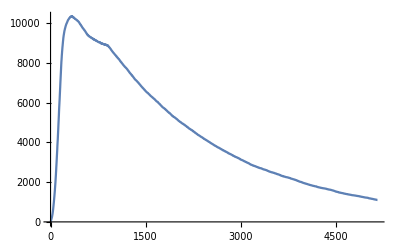

```mathematica
bactData=Table[data[[i]][[5]],{i,1,T}];
immuneData=Table[data[[i]][[6]],{i,1,T}];
ABData=Table[data[[i]][[7]],{i,1,T}];
CSData=Table[data[[i]][[8]],{i,1,T}];
ListLinePlot[{immuneData},PlotRange->All]
```

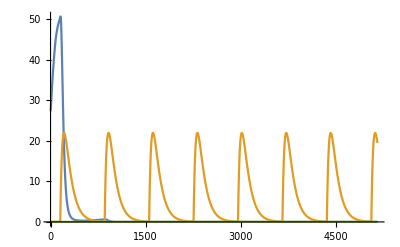

```mathematica
ListLinePlot[{bactData,ABData,CSData},PlotRange->All]
```

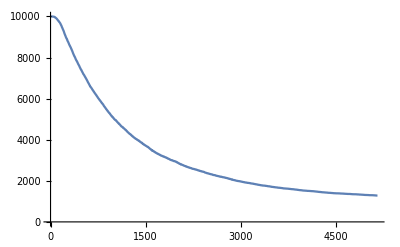

```mathematica
healthyCellData =Table[data[[i]][[2]],{i,1,T}];
ListLinePlot[{healthyCellData},PlotRange->All]
```

## Antibiotic treatment with corticosteroids

```mathematica
T=5150
```

5150

```mathematica
dataCStrue = Import["C:\\Users\\Juhász Nóra\\Documents\\HAL-master\\CorticosteroidsAntibiotics\\output\\StaphyloExperiments\\steroidBoostedAB\\Out.csv","Data"];
```

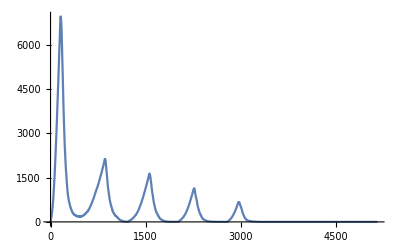

```mathematica
bactData=Table[dataCStrue[[i]][[5]],{i,1,T}];
immuneData=Table[dataCStrue[[i]][[6]],{i,1,T}];
ABData=Table[dataCStrue[[i]][[7]],{i,1,T}];
CSData=Table[dataCStrue[[i]][[8]],{i,1,T}];
ListLinePlot[{immuneData},PlotRange->All]
```

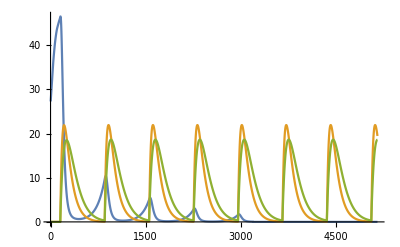

```mathematica
ListLinePlot[{bactData,ABData,CSData}, PlotRange->All]
```

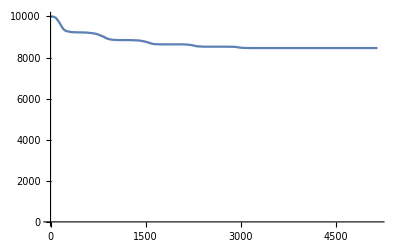

```mathematica
healthyCellData =Table[dataCStrue[[i]][[2]],{i,1,T}];
ListLinePlot[{healthyCellData},PlotRange->{0,10000}]
```